## QUANTUMA ANALOGIES COMPUTATIONS

### 1. Quantum Corral

Let’s solve the SE of the system:
σ^2/(2ρ) ∇^2 ψ + V(r)ψ = Eψ
with the potential
V(r) = Piecewise[{{0, r<a}, {∞, R≥a}}]
In the code, let’s first fix the size of the cell

```mathematica
a = 1;
```

from boundary conditions, with  k=(2 ρ)/σ^2 E , we find a single solution to this equation give
ψ(r) = A_n J_0(k_(0n) r)	; 	K_(0n) = (χ_(0n))/a
where

```mathematica
k[n_]:=BesselJZero[0,n]/a
```

```mathematica
A[n_]:=2/(a^2 BesselJ[1,BesselJZero[0,n]])∫_0^a BesselJ[0,k[n] r]r ⅆr
```

```mathematica
ψ[r_,n_]:=BesselJ[0,k[n]r]
```

Some of this solutions looks like

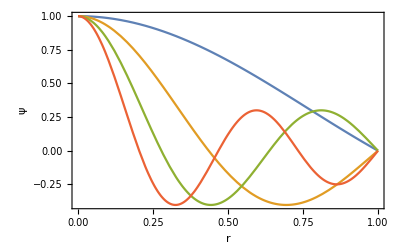

```mathematica
Plot[{ψ[x,1],ψ[x,2], ψ[x,3], ψ[x,4]},{x,0,a},
Frame->True,
FrameLabel->{{"ψ",None},{"r",None}}]
```

The general solution is therefore

```mathematica
Ψ [r_]:= ∑_(n=1)^10 ψ[r,n]
```

which looks like

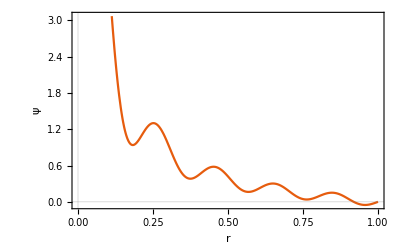

```mathematica
Plot[Ψ[r],{r,0,a},Frame->True,FrameLabel->{{"ψ",None},{"r",None}}, PlotTheme-> "Scientific"]
```

so the amplitude of probability gives

```mathematica
P[r_,n_]:=ψ[r,n]^2
```

we can plot it too

```mathematica
RevolutionPlot3D[P[r,2],{r,0,a}]
```

-Graphics3D-

Now, the quantum potential for this  is

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
Q[r_,n_]:=-ND[ψ[x,n],{x,2},r]/ψ[r,n]
```

which looks like

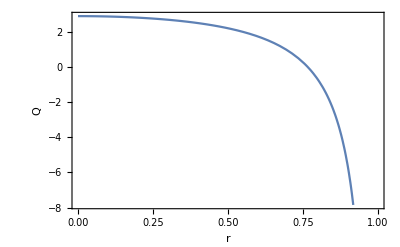

```mathematica
Plot[{Q[r,1]},{r,0,a},
Frame->True,
FrameLabel->{{"Q",None},{"r",None}}]
```

With this, the quantum force is

```mathematica
Fq[r_,n_]:=-ND[Q[x,n],x,r]
```

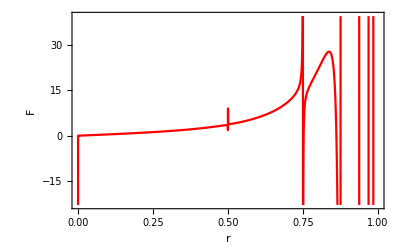

```mathematica
Plot[{Fq[r,1]},{r,0,a},
Frame->True,
PlotStyle->Red,
FrameLabel->{{"F",None},{"r",None}}]
```